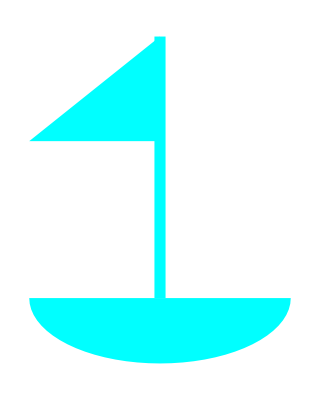

{0.,1.85,3.7,5.55,7.4,9.25}

{{{0.,0},{0.4625,-0.5},{1.3875,-0.5},{1.85,0}},{{1.85,0},{2.3125,-0.5},{3.2375,-0.5},{3.7,0}},{{3.7,0},{4.1625,-0.5},{5.0875,-0.5},{5.55,0}},{{5.55,0},{6.0125,-0.5},{6.9375,-0.5},{7.4,0}},{{7.4,0},{7.8625,-0.5},{8.7875,-0.5},{9.25,0}},{{9.25,0},{9.7125,-0.5},{10.6375,-0.5},{11.1,0}},{{11.1,0},{11.5625,-0.5},{12.4875,-0.5},{12.95,0}},{{12.95,0},{13.4125,-0.5},{14.3375,-0.5},{14.8,0}},{{14.8,0},{15.2625,-0.5},{16.1875,-0.5},{16.65,0}},{{16.65,0},{17.1125,-0.5},{18.0375,-0.5},{18.5,0}},{{18.5,0},{18.9625,-0.5},{19.8875,-0.5},{20.35,0}},{{20.35,0},{22.2,-4},{-1.85,-4},{0,0}}}

{{0.,0},{0.,0},{0.4625,-0.5},{1.3875,-0.5},{1.85,0},{1.85,0},{1.85,0},{1.85,0},{2.3125,-0.5},{3.2375,-0.5},{3.7,0},{3.7,0},{3.7,0},{3.7,0},{4.1625,-0.5},{5.0875,-0.5},{5.55,0},{5.55,0},{5.55,0},{5.55,0},{6.0125,-0.5},{6.9375,-0.5},{7.4,0},{7.4,0},{7.4,0},{7.4,0},{7.8625,-0.5},{8.7875,-0.5},{9.25,0},{9.25,0},{9.25,0},{9.25,0},{9.7125,-0.5},{10.6375,-0.5},{11.1,0},{11.1,0},{11.1,0},{11.1,0},{11.5625,-0.5},{12.4875,-0.5},{12.95,0},{12.95,0},{12.95,0},{12.95,0},{13.4125,-0.5},{14.3375,-0.5},{14.8,0},{14.8,0},{14.8,0},{14.8,0},{15.2625,-0.5},{16.1875,-0.5},{16.65,0},{16.65,0},{16.65,0},{16.65,0},{17.1125,-0.5},{18.0375,-0.5},{18.5,0},{18.5,0},{18.5,0},{18.5,0},{18.9625,-0.5},{19.8875,-0.5},{20.35,0},{20.35,0},{20.35,0},{22.2,-4},{-1.85,-4},{0,0}}

{{{0.,0},{0.4625,-0.5},{1.3875,-0.5},{1.85,0}},{{1.85,0},{2.3125,-0.5},{3.2375,-0.5},{3.7,0}},{{3.7,0},{4.1625,-0.5},{5.0875,-0.5},{5.55,0}},{{5.55,0},{6.0125,-0.5},{6.9375,-0.5},{7.4,0}},{{7.4,0},{7.8625,-0.5},{8.7875,-0.5},{9.25,0}},{{9.25,0},{9.7125,-0.5},{10.6375,-0.5},{11.1,0}},{{11.1,0},{11.5625,-0.5},{12.4875,-0.5},{12.95,0}},{{12.95,0},{13.4125,-0.5},{14.3375,-0.5},{14.8,0}},{{14.8,0},{15.2625,-0.5},{16.1875,-0.5},{16.65,0}},{{16.65,0},{17.1125,-0.5},{18.0375,-0.5},{18.5,0}},{{18.5,0},{18.9625,-0.5},{19.8875,-0.5},{20.35,0}},{{20.35,0},{22.2,-4},{-1.85,-4},{0,0}}}

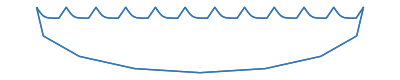

```mathematica
drawBoat[{x_,y_, hue_}] := {Hue[hue,1,1], Disk[{x,y},{1, .5}, {Pi, 2*Pi}], Thickness[0.02],Line[{{0,0},{0,2}}], Triangle[{{0, 1.2},{-1, 1.2},{0,2}}]}

Graphics[drawBoat[{0,0,.5}]]

Table[x,{x, 0, 10, 1.85}]

Append[Table[{{x*1.85,0}, {1.85*(x+.25),-.5},{1.85*(x+.75),-.5}, {(x+1)*1.85,0}}, {x, 0, 10, 1}], {{20.35,0},{12*1.85, -4}, {-1*1.85, -4}, {0,0}}]

FlattenAt[Append[Table[{{x*1.85,0},{x*1.85,0}, {1.85*(x+.25),-.5},{1.85*(x+.75),-.5}, {(x+1)*1.85,0}, {(x+1)*1.85,0}}, {x, 0, 10, 1}], {{20.35,0},{12*1.85, -4}, {-1*1.85, -4}, {0,0}}], Table[{a}, {a,1,12,1}]]

ArrayFlatten[Append[Table[{{x*1.85,0}, {1.85*(x+.25),-.5},{1.85*(x+.75),-.5}, {(x+1)*1.85,0}}, {x, 0, 10, 1}], {{20.35,0},{12*1.85, -4}, {-1*1.85, -4}, {0,0}}]]

drawWaves[{y_, offset_}] := {Hue[0.58,0.71,0.7], BezierCurve[
FlattenAt[Append[Table[{{x*1.85,0}, {1.85*(x+.25),-.5}, {1.85*(x+.25),-.5},{1.85*(x+.75),-.5},{1.85*(x+.75),-.5}, {(x+1)*1.85,0}}, {x, 0, 10, 1}], {{20.35,0},{12*1.85, -4}, {-1*1.85, -4}, {0,0}}], Table[{a}, {a,1,12,1}]]
]}

Graphics[{drawWaves[{0, 0}],drawWaves[{.5, .5}]}]

drawSand[] := {Yellow}
```